```mathematica
ClearAll["Global`*"]
```

First we setup some basic stuff (maybe move these to a package?)

```mathematica
Needs["GraphStore`"]
ex[s_]:="http://example.org/"<>s
msc[code_] := "http://msc2010.org/resources/MSC/2010/" <> code;
RDFGraph[rdf_]:=rdf // SPARQLSelect[
RDFTriple[SPARQLVariable["s"], SPARQLVariable["p"], SPARQLVariable["o"]]
] // Map[Function[
DirectedEdge[#s,#o,#p]
]]//Graph
TooltipGraph[graph_]:=GraphPlot[graph, 
VertexLabels->MapIndexed[#->Placed[Tooltip[" ",#],Center]&,graph//VertexList], 
EdgeLabels->MapIndexed[#->Placed[Tooltip["+",#[[3]]],Center]&,graph//EdgeList] (* the + on the edge is to indicate where to hover *)
]
```

```mathematica
msc2020 := Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"MSC_2020.csv"}], "CSV"][[2;;]]
msc2020filtered:={StringTake[#[[1]], 2]<>"Axx", #[[2]]}&/@Select[msc2020, StringMatchQ[ToString[#[[1]]], RegularExpression["\d\d[\-a-zA-z]\d\d"]]&]
msc2020gathered:={#[[1,1]],StringSplit[#[[All,2]], " "]//Flatten}&/@GatherBy[msc2020filtered, #[[1]]&]
classifier:=Classify[Function[word,word->#[[1]]]/@#[[2]]&/@msc2020gathered//Flatten]
classifier["Mathematics,", "TopProbabilities"]
```

{01Axx→0.733958,00Axx→0.127811,97Axx→0.0989389}

```mathematica
files:=FileNames["*.pdf", ParentDirectory[NotebookDirectory[]]<>"/modules"]
text:={StringTake[#,StringPosition[#,"Module M"][[1,2]];;StringPosition[#,"Module "][[1,2]]+7],Import[#,"Plaintext"]}&/@files
modules:={#[[1]],Select[StringSplit[StringDelete[StringTake[#[[2]], StringPosition[#[[2]],"SYLLABUS PLAN - summary of the structure and academic content of the module"][[1,2]]+2;;StringPosition[#[[2]],"LEARNING AND TEACHING"][[1,1]]-2], Except[LetterCharacter|" "|"-"|"\n"]]," "|"-"|"\n"],Function[p1,StringLength[p1]!=0] ]}&/@text
```

```mathematica
(*The line below took about 5 hours to run so it is cached in data.m (probably because I was silly with classifier:=)*)
(*classified:={#[[1]],Function[p1,classifier[p1, "TopProbabilities"][[1]]]/@#[[2]]}&/@modules;*)
classified:=Import[NotebookDirectory[]<>"data.m"];
classifiedList:={#[[1]],Function[p1,Apply[List,p1]]/@#[[2]]}&/@classified;
```

```mathematica
thing={{"35Axx",1.336464}, {"42Axx",0.968698}, {"11Axx",0.760049}, {"26Axx",0.423802}, {"34Axx",0.282966}};
Function[p1,{p1[[1]],p1[[2]]/Total[thing[[All,2]]]}]/@thing
```

{{35Axx,0.354314},{42Axx,0.256814},{11Axx,0.201499},{26Axx,0.112355},{34Axx,0.0750179}}

```mathematica
classTotals:={#[[1]],Sort[Apply[List,Function[p2,{p2[[1,1]],Total[p2[[All,2]]]}]/@GroupBy[#[[2]], Function[p1,p1[[1]]]]],Function[{l,r},l[[2]]>r[[2]]]]}&/@classifiedList;
(*Just adding it would obviously prioritise larger descriptions (if we cut by some threshold) so we then normalise the data*)
classNormed:={#[[1]],Function[p1,{p1[[1]],p1[[2]]/Total[#[[2,All,2]]]}]/@#[[2]]}&/@classTotals;
(*Remove items smaller than 0.05 (arbitrarily picked cutoff)*)
trimmed:={#[[1]],Select[#[[2]],Function[p1,p1[[2]]>0.05]][[All,1]]}&/@classNormed;
trimmed
```

{{MTH1000,{65Axx,97Axx,11Axx,42Axx,34Axx,35Axx,45Axx,05Axx}},{MTH1001,{40Axx,46Axx,03Axx,20Axx,11Axx}},{MTH1002,{34Axx,45Axx,13Axx,15Axx,40Axx,44Axx,41Axx,32Axx}},{MTH1003,{31Axx,54Axx,40Axx,47Axx,00Axx,83Axx}},{MTH1004,{30Axx,41Axx,94Axx,60Axx,62Axx,52Axx}},{MTH2003,{35Axx,39Axx,42Axx,65Axx,34Axx}},{MTH2004,{76Axx,12Axx,31Axx,40Axx,34Axx,39Axx}},{MTH2005,{40Axx,65Axx,35Axx,34Axx}},{MTH2006,{41Axx,62Axx,91Axx,30Axx,34Axx,81Axx,65Axx,82Axx}},{MTH2008,{26Axx,40Axx}},{MTH2009,{45Axx,26Axx,30Axx,32Axx}},{MTH2010,{20Axx,13Axx,12Axx,45Axx,32Axx}},{MTH2011,{47Axx,46Axx,37Axx,15Axx}},{MTH3001,{76Axx,80Axx,01Axx,31Axx}},{MTH3004,{11Axx,51Axx,68Axx,16Axx,35Axx}},{MTH3006,{03Axx,40Axx,32Axx}},{MTH3007,{76Axx,39Axx,83Axx,91Axx}},{MTH3008,{35Axx,39Axx,65Axx,37Axx,44Axx,47Axx}},{MTH3011,{93Axx,40Axx,47Axx,30Axx,49Axx}},{MTH3013,{34Axx,44Axx,30Axx,51Axx,86Axx}},{MTH3019,{01Axx,51Axx,11Axx,60Axx}},{MTH3022,{05Axx,76Axx,94Axx,70Axx,32Axx}},{MTH3024,{60Axx,35Axx,11Axx,62Axx}},{MTH3026,{35Axx,01Axx,68Axx,11Axx,30Axx,65Axx}},{MTH3028,{34Axx,41Axx,35Axx,51Axx,91Axx}},{MTH3030,{41Axx,93Axx,94Axx,34Axx,74Axx,35Axx}},{MTH3038,{12Axx,31Axx,20Axx,11Axx}},{MTH3039,{65Axx,35Axx,52Axx,39Axx,68Axx,55Axx,11Axx,31Axx}},{MTH3040,{28Axx,46Axx,54Axx,26Axx}},{MTH3041,{62Axx,40Axx,18Axx,60Axx,34Axx,68Axx}},{MTH3042,{45Axx,47Axx,39Axx,65Axx,44Axx}},{MTH3045,{68Axx,65Axx,49Axx,44Axx,15Axx,41Axx,82Axx}}}

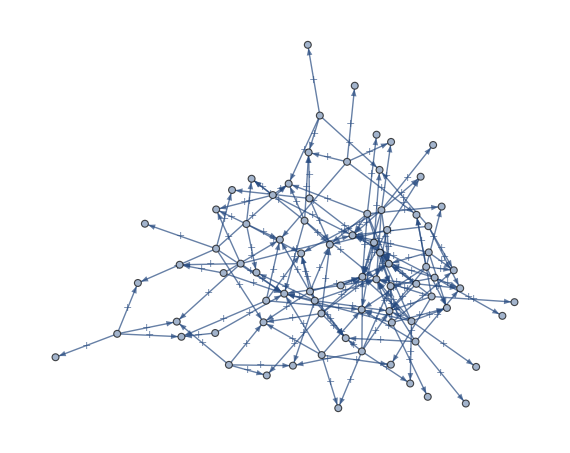

```mathematica
ourGraph:=(Function[code,RDFTriple[ex[#[[1]]],ex["uses"],msc[code]]]/@#[[2]])&/@trimmed//Flatten;
rdfStore:=ourGraph//RDFStore
rdfStore//RDFGraph//TooltipGraph
```

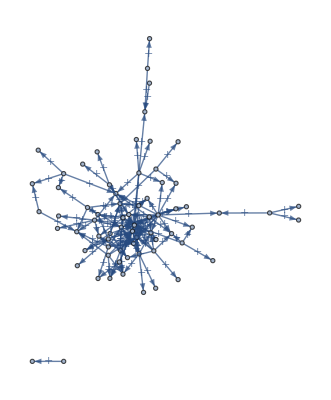

```mathematica
filterOther[store_]:=store//SPARQLSelect[
     RDFTriple[SPARQLVariable["s"], SPARQLVariable["p"], 
      SPARQLVariable["o"]]
     ] // Map[Function[
RDFTriple[#s, #p,(Function[r,StringReplace[#o,r->"2010/"<>StringPart[r,{6,7}]<>"Axx"]]/@StringCases[#o, RegularExpression["2010/\d\d[a-zA-Z_\- ]\d\d"]] // Append[#o])[[1]]]
     ]]//Select[(#[[2]]==ex["uses"]&&#[[1]]!=ex["MTH3035"])&]//DeleteDuplicates;(*Remove all links that aren't uses and remove Group Project as it is so varied*)
(*My CloudImport stopped working so I just downloaded them locally*)
g1=filterOther[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"other_data/ben_white.m"}],"WL"]];(*Ben White - https://www.wolframcloud.com/env/e5c61039-81b9-49d6-8032-46e848745bd6*)
g2=filterOther[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"other_data/holly_barber.m"}],"WL"]];(*Holly Barber - https://www.wolframcloud.com/obj/6e83321c-6e9e-496b-aa5f-1f4a1a5995d4*)
g3=filterOther[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"other_data/lucie_johnson.m"}],"WL"]];(*Lucie Johnson - https://www.wolframcloud.com/obj/d205a732-06d2-4499-8180-1aa79906a7ef*)
g4=filterOther[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"other_data/luke_garner.m"}],"WL"]];(*Luke Garner - https://www.wolframcloud.com/env/1ff93e1f-5a29-4ba4-a087-0bc56d3f8134*)
g5=filterOther[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"other_data/donovan_tran.m"}],"WL"]]; (*Donovan Tran - https://www.wolframcloud.com/obj/6ce308a9-99eb-4ba4-b91c-4ed313597abd*)
otherGraph:=Flatten[Join[{g1,g2,g3,g4, g5}],{1,2}];
rdfStoreOther=otherGraph//RDFStore;
rdfStoreOther//RDFGraph//TooltipGraph
```

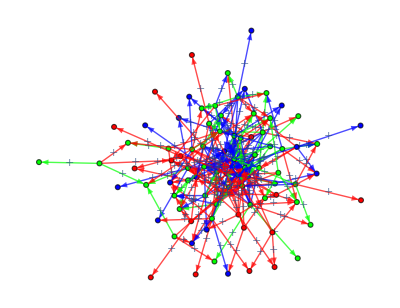

```mathematica
combinedGraph = Join[rdfStore[[1]], rdfStoreOther[[1]]] // DeleteDuplicates // RDFStore//RDFGraph;
intersectGraph = Intersection[rdfStore[[1]], rdfStoreOther[[1]]] // RDFStore // RDFGraph;
HighlightGraph[combinedGraph, {Style[rdfStore//RDFGraph,Red],Style[rdfStoreOther//RDFGraph,Blue], Style[intersectGraph,Green]}] // TooltipGraph
```

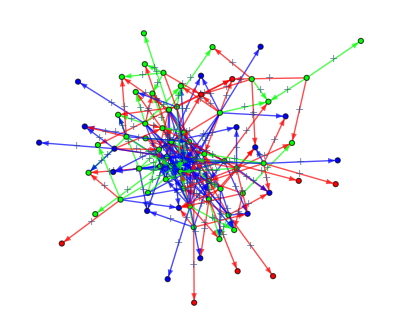

```mathematica
(*Remove all modules from our graph that no one else mentioned as there is no reason to compare them*)
ourFilteredGraph:=Select[ourGraph,MemberQ[otherGraph[[All,1]],#[[1]]]&];
combinedGraph:=Join[ourFilteredGraph,otherGraph]//DeleteDuplicates//RDFStore//RDFGraph;
intersectGraph:=Intersection[ourFilteredGraph,otherGraph]//RDFStore//RDFGraph;
HighlightGraph[combinedGraph,{Style[ourFilteredGraph//RDFStore//RDFGraph,Red],Style[rdfStoreOther//RDFGraph,Blue],Style[intersectGraph,Green]}]//TooltipGraph
```

```mathematica
totalEdges:=Join[ourFilteredGraph,otherGraph]//DeleteDuplicates//Length;
sharedEdges:=Intersection[ourFilteredGraph,otherGraph]//Length;

totalVertices:=Flatten[{ourFilteredGraph[[All,1]],ourFilteredGraph[[All,3]],otherGraph[[All,1]],otherGraph[[All,3]]}]//DeleteDuplicates//Length;
sharedVertices:=Intersection[Flatten[{ourFilteredGraph[[All,1]],ourFilteredGraph[[All,3]]}],Flatten[{otherGraph[[All,1]],otherGraph[[All,3]]}]]//Length;

ourCommunities=FindGraphCommunities[ourFilteredGraph//RDFStore//RDFGraph];
otherCommunities=FindGraphCommunities[rdfStoreOther//RDFGraph];
ScoreClusterRatio[graph1_,graph2_]:=(Select[Function[p1,MemberQ[#[[1]],p1]]/@#[[2]],Function[a,a]]//Length)&/@Select[Flatten[{graph1,graph2},{{2},{1}}],Length[#]==2&]//Total
sharedClusterVertices=(ScoreClusterRatio[ourCommunities,#]&/@Permutations[otherCommunities]//TakeLargest[1])[[1]];

((sharedEdges/totalEdges) + (sharedVertices/totalVertices) + (sharedClusterVertices/totalVertices)) / 3
```

22523/49374

```mathematica
TooltipCommunityGraph[graph_]:=CommunityGraphPlot[graph,FindGraphCommunities[graph], 
VertexLabels->MapIndexed[#->Placed[Tooltip[" ",#],Center]&,graph//VertexList]
]
```

```mathematica
TooltipCommunityGraph[rdfStore//RDFGraph]
```

-Graphics-

Light Green: 3013, 3019, 3028 (Applied Diff Geom, History & Culture, Statistical Inference)
Purple: 1003, 2004, 3001, 3007 (Modelling, Vector Calculus, Weather & Climate, Fluid Dynamics)
Teal: 2010, 3038 (GRF, Galois)
Red: 1001, 2008, 2009, 3006, 3022, 3040 (Structures, Real Analysis, Complex Analysis, Biology & Ecology, GNA, Topology)
Gold: 1004, 3024, 3041 (Probability, Stochastic, Bayesian Stats)
Orange: 2006, 3011, 3030, 3045 (Statistical Modelling, Nonlinear Systems, Climate Change, Statistical Computing)
Yellow: 1000, 2003, 2005, 3004, 3026, 3039 (Foundations, Differential Equations, Modelling Theory & Practice, Number Theory, Cryptography, CND)
Dark Green: 1002, 2011, 3008, 3042 (Methods, Linear Algebra, Partial Differential Equations, Integral Equations)

```mathematica
(*FindGraphCommunities[rdfStore//RDFGraph]*)
KCoreComponents[rdfStore//RDFGraph,3]
```

{{http://example.org/MTH1000,http://msc2010.org/resources/MSC/2010/65Axx,http://msc2010.org/resources/MSC/2010/11Axx,http://msc2010.org/resources/MSC/2010/34Axx,http://msc2010.org/resources/MSC/2010/35Axx,http://msc2010.org/resources/MSC/2010/45Axx,http://example.org/MTH1001,http://msc2010.org/resources/MSC/2010/40Axx,http://msc2010.org/resources/MSC/2010/20Axx,http://example.org/MTH1002,http://msc2010.org/resources/MSC/2010/44Axx,http://msc2010.org/resources/MSC/2010/41Axx,http://msc2010.org/resources/MSC/2010/32Axx,http://example.org/MTH1003,http://msc2010.org/resources/MSC/2010/31Axx,http://msc2010.org/resources/MSC/2010/47Axx,http://example.org/MTH1004,http://msc2010.org/resources/MSC/2010/30Axx,http://msc2010.org/resources/MSC/2010/94Axx,http://msc2010.org/resources/MSC/2010/60Axx,http://msc2010.org/resources/MSC/2010/62Axx,http://example.org/MTH2003,http://msc2010.org/resources/MSC/2010/39Axx,http://example.org/MTH2004,http://msc2010.org/resources/MSC/2010/76Axx,http://msc2010.org/resources/MSC/2010/12Axx,http://example.org/MTH2005,http://example.org/MTH2006,http://msc2010.org/resources/MSC/2010/91Axx,http://example.org/MTH2009,http://example.org/MTH2010,http://example.org/MTH3001,http://msc2010.org/resources/MSC/2010/01Axx,http://example.org/MTH3004,http://msc2010.org/resources/MSC/2010/51Axx,http://msc2010.org/resources/MSC/2010/68Axx,http://example.org/MTH3007,http://example.org/MTH3008,http://example.org/MTH3011,http://example.org/MTH3013,http://example.org/MTH3019,http://example.org/MTH3022,http://example.org/MTH3024,http://example.org/MTH3026,http://example.org/MTH3028,http://example.org/MTH3030,http://example.org/MTH3038,http://example.org/MTH3039,http://example.org/MTH3041,http://example.org/MTH3042,http://example.org/MTH3045}}

```mathematica
TooltipCommunityGraph[rdfStoreOther//RDFGraph]
```

-Graphics-

Red : msc03, msc15, msc41, MTH1004, msc60, msc62, msc68, MTH2006, MTH3022, msc05,  MTH3024, msc82, msc97, MTH3028, msc98.
Yellow : msc40, MTH1002, msc26, msc34, MTH2003, msc42, MTH2008, MTH3030, msc86, msc33, MTH2009, msc32, msc30, msc91, MTH3040, msc54, msc51.
Purple : MTH1001, msc11, msc20, msc14, MTH2011, msc08, MTH2010, MTH3004, MTH3026, msc94, MTH3038, msc12, msc13, msc06.
Orange : msc35, msc46, MTH1003, msc83, msc65, msc00, MTH3006, msc37, msc92, MTH2005.
Green : MTH2004, msc74, msc76, msc78, msc53, MTH3007, MTH3001, msc80.
Brown : MTH3042, msc44, msc45, msc47.
Cyan : MTH3019, msc01.

```mathematica
KCoreComponents[rdfStoreOther//RDFGraph,4]
```

{{http://example.org/MTH1001,http://msc2010.org/resources/MSC/2010/03Axx,http://msc2010.org/resources/MSC/2010/15Axx,http://msc2010.org/resources/MSC/2010/40Axx,http://example.org/MTH1002,http://msc2010.org/resources/MSC/2010/26Axx,http://msc2010.org/resources/MSC/2010/34Axx,http://msc2010.org/resources/MSC/2010/41Axx,http://example.org/MTH2003,http://example.org/MTH2006,http://example.org/MTH3022,http://example.org/MTH3024,http://msc2010.org/resources/MSC/2010/97Axx,http://example.org/MTH1003,http://example.org/MTH2009}}

```mathematica
CompareLaplacian[graph1_, graph2_] := 
 Module[{ev1, ev2, m, ls1, ls2, penalty},
  ev1 = graph1 // UndirectedGraph // KirchhoffMatrix // Normal // N //
      Eigenvalues // Sort;
  ev2 = graph2 // UndirectedGraph // KirchhoffMatrix // Normal // N //
      Eigenvalues // Sort;
  m = Max[{Length[ev1], Length[ev2]}];
  ls1 = PadRight[ev1, m];
  ls2 = PadRight[ev2, m];
  penalty = Abs[Length[ev1] - Length[ev2]];
  ManhattanDistance[ls1, ls2] + penalty
  ]
CompareAdjacency[graph1_, graph2_] := 
 Module[{ev1, ev2, m, ls1, ls2, penalty},
  ev1 = graph1 // UndirectedGraph // AdjacencyMatrix // Normal // N //
      Eigenvalues // Sort;
  ev2 = graph2 // UndirectedGraph // AdjacencyMatrix // Normal // N //
      Eigenvalues // Sort;
  m = Max[{Length[ev1], Length[ev2]}];
  ls1 = PadRight[ev1, m];
  ls2 = PadRight[ev2, m];
  penalty = Abs[Length[ev1] - Length[ev2]];
  ManhattanDistance[ls1, ls2] + penalty
  ]
CompareLaplacian[ourFilteredGraph//RDFGraph, otherGraph//RDFGraph]
CompareAdjacency[ourFilteredGraph//RDFGraph,otherGraph//RDFGraph]
```

66.661

28.6613

```mathematica
GenerateGraph[cutoff_]:=Select[(Function[code,RDFTriple[ex[#[[1]]],ex["uses"],msc[code]]]/@#[[2]])&/@({#[[1]],Select[#[[2]],Function[p1,p1[[2]]>cutoff]][[All,1]]}&/@classNormed)//Flatten,MemberQ[otherGraph[[All,1]],#[[1]]]&]//RDFGraph;
CutoffLaplacian[cutoff_]:=CompareLaplacian[GenerateGraph[cutoff],otherGraph//RDFGraph];
CutoffAdjacency[cutoff_]:=CompareAdjacency[GenerateGraph[cutoff],otherGraph//RDFGraph];
Plot[{CutoffLaplacian[x],CutoffAdjacency[x]},{x, 0.01, 0.1},PlotLabels->{Style["Laplacian",14],Style["Adjacency",14]},Frame->{True,True,False,False},FrameLabel->{Style["Probability Cutoff",14],Style["Spectral Distance",14]}]
```

-Graphics-